```mathematica
NthDividedDiff[x0_,f0_,startindex_,endindex_]:=
Module[{x=x0,f=f0,i=startindex,j=endindex,answer},
If[i==j,Return[f[[i]]],
answer=(NthDividedDiff[x,f,i+1,j]-NthDividedDiff[x,f,i,j-1])/(x[[j]]-x[[i]]);Return[answer]];];

x={0,1,3};
f={1,3,55};
NthDividedDiff[x,f,1,2]
```

2

```mathematica
NewtonDDPoly[x0_,f0_]:=
Module[{x1=x0,f=f0,n,newtonpoly,k,j},
n=Length[x1];
newtonpoly[y_]=0;
For[i=1,i≤n,i++,prod[y_]=1;
For[k=1,k≤i-1,k++,prod[y_]=prod[y]*(y-x1[[k]])];
newtonpoly[y_]=newtonpoly[y]+NthDividedDiff[x1,f,1,i]*prod[y]];
Return[newtonpoly[y]];];
nodes={0,1,3};
values={1,3,55};
Newtonpoly[y_]=NewtonDDPoly[nodes,values]
```

1+2 y+8 (-1+y) y

```mathematica
Newtonpoly[y_]=Simplify[Newtonpoly[y]]
```

1-6 y+8 y^2

```mathematica
nodes={0.0,0.1,0.2,0.3,0.4};
values={1,1.095,1.179,1.251,1.310};
Newtonpoly[y_]=NewtonDDPoly[nodes,values]
```

1+0.95 (0.+y)-0.55 (-0.1+y) (0.+y)-0.166667 (-0.2+y) (-0.1+y) (0.+y)+3.47014×10^-13 (-0.3+y) (-0.2+y) (-0.1+y) (0.+y)

```mathematica
Newtonpoly[y_]=Simplify[Newtonpoly[y]]
```

1.+1.00167 y-0.5 y^2-0.166667 y^3+3.47014×10^-13 y^4

```mathematica
Newtonpoly[0.15]
```

1.13844

```mathematica
Newtonpoly[0.25]
```

1.21656

```mathematica
nodes={0.5,1.5,3.0,5.0,6.5,8.0};
values={1.625,5.875,31.0,131.0,282.125,521.0};
Newtonpoly[y_]=NewtonDDPoly[nodes,values]
```

Set::write: Tag Plus in (1297.84-4081.54 y+3492.21 y^2-1098.38 y^3+144.209 y^4-6.71917 y^5)[y_] is Protected.

1.625+4.25 (-0.5+y)+5. (-1.5+y) (-0.5+y)+1. (-3.+y) (-1.5+y) (-0.5+y)

```mathematica
Newtonpoly=Simplify[Newtonpoly[y]]
```

(1297.84-4081.54 y+3492.21 y^2-1098.38 y^3+144.209 y^4-6.71917 y^5)[y][y][y][y][y][y][y]

```mathematica
nodes={0,Pi/4,Pi/2};
values={N[Sin[0]],N[Sin[Pi/4]],N[Sin[Pi/2]]};
Newtonpoly[y_]=NewtonDDPoly[nodes,values]
```

Set::write: Tag Plus in (1297.84-4081.54 y+3492.21 y^2-1098.38 y^3+144.209 y^4-6.71917 y^5)[y][y][y][y][y][y][y][y_] is Protected.

0.+0.900316 y-0.335749 y (-π/4+y)

```mathematica
Newtonpoly=Simplify[Newtonpoly[y]]
```

(1297.84-4081.54 y+3492.21 y^2-1098.38 y^3+144.209 y^4-6.71917 y^5)[y][y][y][y][y][y][y][y]

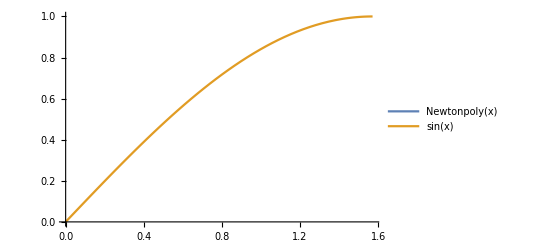

```mathematica
Plot[{Newtonpoly[x],Sin[x]},{x,0,Pi/2},Ticks->{Range[0.10]},PlotLegends->"Expressions"]
```